```mathematica
MargaretdEdx5Points=Import["C:\\Users\\jose2\\Desktop\\Werk\\Técnico\\6 Ano 1 Semestre\\Liliana_Pablo\\Graph Reader\\Nova pasta\\dEdx_Margaret_v2.csv"];
dEdx5=Interpolation[MargaretdEdx5Points,InterpolationOrder->1];
MargaretQHat5Points=Import["C:\\Users\\jose2\\Desktop\\Werk\\Técnico\\6 Ano 1 Semestre\\Liliana_Pablo\\Graph Reader\\qhat_5_v2.csv"];
QHat5=Interpolation[MargaretQHat5Points,InterpolationOrder->1];

GeVtofm=0.1973; (*1 GeV = GeVtofm / 1 fm -- should use more algarisms?*)
Subscript[v, perp]=1.0; (*adimensional*)
Subscript[v, paral]=0; (*adimensional*)
v=√(Subscript[v, perp]^2+Subscript[v, paral]^2); (*adimensional - should v always equal 1?*)
Subscript[N, c]=3;
g=1.0; (*adimensional*) (*If Q is different then why shouldn't g be*)
T=1.0; 
Subscript[Q, 1]=2.0;  (*GeV*)
Subscript[Q, 2]=2.0;(*GeV*)
m=0.2; (*GeV*)

stoppingPowerPrefactor=-1/(v*T)*g^4/4*(Subscript[N, c]^2-1);
qHatPrefactor=g^4/2*(Subscript[N, c]^2-1)/v^3;

regConstant=N[4*Exp[-2*EulerGamma-1]];
preFactor[Q_]:=Q^2/(g^2*Subscript[N, c])
radius[τ_,τʹ_,φ_,ϕ_]:=√((Subscript[v, perp]*(τ-τʹ)+(τʹ*Cos[φ]-τ*Cos[ϕ]))^2+(τʹ*Sin[φ]-τ*Sin[ϕ])^2)(*GeV^-2*) (*0 ⩽ r ⩽√((τ-τʹ)^2((1+Subscript[v, perp])^2+1))=(cond.)0.044*)
MVmr[τ_,τʹ_,φ_,ϕ_]:=m*radius[τ,τʹ,φ,ϕ]
MVArg1[mr_]:=mr*BesselK[1,mr]
MVarg2[mr_]:=2*BesselK[0,mr]
MVLog[mr_]:=Log[regConstant/mr^2+E]
MVArgExp[mr_,Q_]:=Q^2/m^2*(MVArg1[mr]-1)
ExpFraction[x_]:=(1-Exp[x])/x
hMV[mr_,Q_]:=-preFactor[Q]*MVArg1[mr]/MVLog[mr]*ExpFraction[MVArgExp[mr,Q]]
(*could it be made faster if it didn't have to calculate MVArg1 twice?*)
GMV[mr_,Q_]:=preFactor[Q]*(MVArg1[mr]-MVarg2[mr])/MVLog[mr]*ExpFraction[MVArgExp[mr,Q]]

integrandStoppingPowerMV[mr_,φ_,ϕ_]:=GMV[mr,Subscript[Q, 1]]*GMV[mr,Subscript[Q, 2]]*(Subscript[v, paral]^2+Subscript[v, perp]^2*Sin[φ]*Sin[ϕ])+hMV[mr,Subscript[Q, 1]]*hMV[mr,Subscript[Q, 2]]*(Subscript[v, paral]^2-Subscript[v, perp]^2*Sin[φ]*Sin[ϕ]) (*completely symmetric under φ↔ϕ *)
stoppingPowerMV[τ_]:=stoppingPowerPrefactor*NIntegrate[integrandStoppingPowerMV[MVmr[τ,τʹ,φ,ϕ],φ,ϕ],{φ,0,2π},{ϕ,0,2π},{τʹ,0,τ}]

integrandQHatMV[mr_,φ_,ϕ_]:=(1+v^2)*GMV[mr,Subscript[Q, 1]]*GMV[mr,Subscript[Q, 2]]*(Subscript[v, paral]^2*Cos[φ-ϕ]+Subscript[v, perp]^2*(Cos[φ]*Cos[ϕ]+1))-hMV[mr,Subscript[Q, 1]]*hMV[mr,Subscript[Q, 2]]*((1-v^2)*(Subscript[v, paral]^2*Cos[φ-ϕ]+Subscript[v, perp]^2*(Cos[φ]*Cos[ϕ]-1))+2*Subscript[v, perp]*v^2*(Cos[φ]+Cos[ϕ]))(*completely symmetric under φ↔ϕ *)
qHatMV[τ_]:=qHatPrefactor*NIntegrate[integrandQHatMV[MVmr[τ,τʹ,φ,ϕ],φ,ϕ],{φ,0,2π},{ϕ,0,2π},{τʹ,0,τ}]
```

```mathematica
(*stoppingPowerMV[0.02/GeVtofm]*GeVtofm
stoppingPowerMV[0.04/GeVtofm]*GeVtofm
stoppingPowerMV[0.06/GeVtofm]*GeVtofm
stoppingPowerMV[0.08/GeVtofm]*GeVtofm
stoppingPowerMV[0.1/GeVtofm]*GeVtofm*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0222092 and 4.15772×10^-8 for the integral and error estimates.

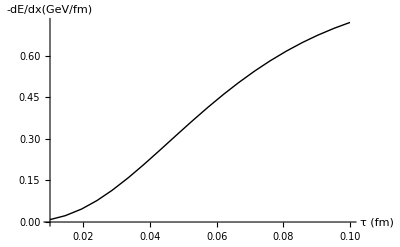

```mathematica
dEdxNarrowLin=Plot[-stoppingPowerMV[τ/GeVtofm]*GeVtofm,{τ,0.01,0.1},PlotPoints->20,MaxRecursion->0,AxesLabel->{"τ (fm)","-dE/dx(GeV/fm)"},PlotStyle->{Thick,Black}]
```

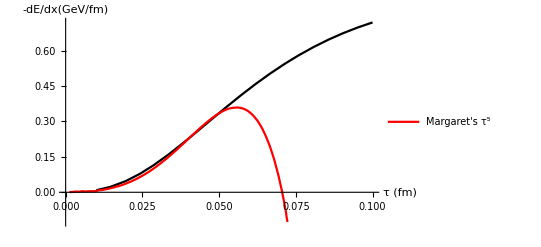

```mathematica
Show[dEdxNarrowLin,Plot[dEdx5[τ],{τ,0.00122,0.07228},PlotLegends->{"Margaret's τ^5"},PlotStyle->{Thick,Red}],PlotRange->{{0,0.1},All},AxesOrigin->{0,0}]
```

```mathematica
(*qHatMV[0.02/GeVtofm]*GeVtofm
qHatMV[0.04/GeVtofm]*GeVtofm
qHatMV[0.06/GeVtofm]*GeVtofm
qHatMV[0.08/GeVtofm]*GeVtofm
qHatMV[0.1/GeVtofm]*GeVtofm*)
```

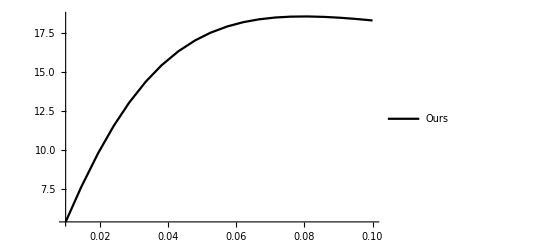

```mathematica
qHatNarrowLinPlot=Plot[qHatMV[τ/GeVtofm]*GeVtofm,{τ,0.01,0.1},PlotPoints->20,MaxRecursion->0,PlotStyle->{Thick,Black},PlotLegends->{"Ours"}]
```

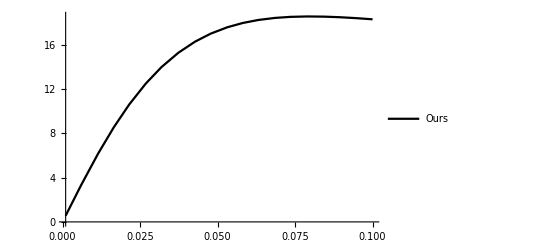

```mathematica
qHatNarrowLinPlot2=Plot[qHatMV[τ/GeVtofm]*GeVtofm,{τ,0.001,0.1},PlotPoints->20,MaxRecursion->0,PlotStyle->{Thick,Black},PlotLegends->{"Ours"}]
```

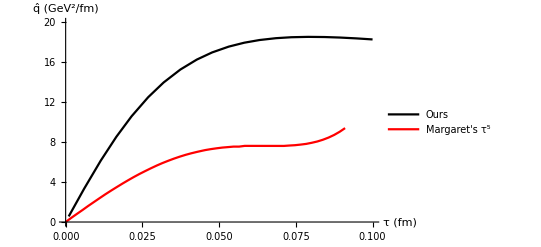

```mathematica
Show[qHatNarrowLinPlot2,Plot[QHat5[τ],{τ,0,0.09105},PlotLegends->{"Margaret's τ^5"},PlotStyle->{Thick,Red}],PlotRange->{{0,0.1},{0,20}},AxesOrigin->{0,0},AxesLabel->{"τ (fm)",OverHat[q]"(GeV^2/fm)"}]
```